# 7+1: the octonions and the Clifford algebra of 7+1 spacetime

## A real realization of the octonions and a real 16×16 realization of the Clifford algebra, built from — and mirroring — the split octonions and the 16×16 Dirac matrices of 4+4.nb

Prepared for Nash's 7+1 project (github.com/once-ere/7+1). Wolfram Language 15.0.1. This notebook was generated by tools/make_7p1_nb.py and evaluated in Wolfram 15.0.1; every claim in it is checked by a cell of the form check["name", test].

Summary. Starting from the real 8×8 matrices τ[A] and the real 16×16 Dirac matrices T16[A] of 4+4.nb (split octonions and the Clifford algebra Cl(4,4)), this notebook constructs: (i) a real realization of the octonions, τO[A] = τ[A] for A ≤ 3 and τO[A] = τ[A].σ for A ≥ 4, whose multiplication table is produced by exactly the same vielbein formula as the split-octonion table of 4+4.nb; (ii) the Clifford algebra of 7+1 spacetime (x0 = time = the octonion unit, x1 … x7 = space) as REAL 16×16 matrices Γ17[A] built from T16; this is possible because the octonions’ own quadratic form Re(x x) = x0.b2 − x1.b2 − … − x7.b2 has signature (1,7) and Cl(1,7) ≅ ℝ(16); (iii) a proof that with the opposite overall sign (the sign convention of 4+4.nb, metric η71) no real 16×16 realization exists, because Cl(7,1) ≅ ℍ(8); for that convention the notebook gives the minimal complexification Γ71 (the exact block form of T16 with a single factor i) and a real 32×32 realization; (iv) examples: Fano plane, Moufang identities, the eight-square identity, Cayley–Dickson doubling, so(1,7), a boost and a rotation, the 7+1 Dirac operator, real on-shell spinor amplitudes, real massless and massive spinor fields, and the classification of all nine signatures p+q = 8. All checks are collected in the last section.

## 0. How to use this notebook

Evaluate the whole notebook in order (Evaluation ▸ Evaluate Notebook). Each verification is a cell check["name", test]; it prints name → True and stores the result in the association checks. Section 6 lists all checks; allChecksPassed must be True.

The notebook has its own private context (CellContext → Notebook), so its symbols cannot collide with the symbols of 4+4.nb (which protects, for example, unit and hUSE) when both notebooks are open.

Index conventions: A, B, K, L run over 0 … 7 and label the coordinates x0 … x7, the octonion units e[0] … e[7] and the generators Γ17[0] … Γ17[7]; i, j run over the imaginary/space values 1 … 7. Mathematica lists are 1-based, hence the frequent [[A+1, B+1]]. The letters C, D, E, I, N, O are built-in Wolfram symbols and are never used as variables here.

```mathematica
{$Version, $Context}
```

{15.0.1 for Microsoft Windows (64-bit) (July 2, 2026),Notebook$$43$40478`}

```mathematica
(* bookkeeping for all verifications in this notebook *)
checks = <||>;
check[name_String, test_] := Module[{r = TrueQ[test]}, AssociateTo[checks, name -> r]; name -> r];
```

## 1. Conventions, coordinates and notation

### 1.1 Coordinates X = {x0, …, x7}

4+4.nb and this notebook use the SAME eight coordinate symbols X = {x0, x1, x2, x3, x4, x5, x6, x7} (never x1, …, x8). Their physical meaning is different:

```mathematica
X = {x0, x1, x2, x3, x4, x5, x6, x7};
Grid[Prepend[{
   {"x0", "hidden space-like dimension", "ordinary time; octonion unit e[0] = 1"},
   {"x1, x2, x3", "ordinary 3-space", "ordinary 3-space; imaginary units e[1], e[2], e[3]"},
   {"x4", "ordinary time", "auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)"},
   {"x5, x6, x7", "3 auxiliary time-like dimensions (superluminal deflating time)", "auxiliary space-like; e[5], e[6], e[7]"}},
  {"coordinate", "meaning in 4+4.nb (signature 4+4)", "meaning in 7+1.nb (signature 7+1)"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

coordinate | meaning in 4+4.nb (signature 4+4) | meaning in 7+1.nb (signature 7+1)
x0 | hidden space-like dimension | ordinary time; octonion unit e[0] = 1
x1, x2, x3 | ordinary 3-space | ordinary 3-space; imaginary units e[1], e[2], e[3]
x4 | ordinary time | auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)
x5, x6, x7 | 3 auxiliary time-like dimensions (superluminal deflating time) | auxiliary space-like; e[5], e[6], e[7]

### 1.2 Metrics and sign conventions

4+4.nb uses the sign convention “space-like = +1, time-like = −1”: η4488 = diag(+1,+1,+1,+1,−1,−1,−1,−1) (x0 … x3 space-like, x4 … x7 time-like), and its Dirac matrices obey T16[A].T16[B] + T16[B].T16[A] = 2 η4488[[A+1,B+1]] ID16. In the same convention the 7+1 metric is η71 = diag(−1,+1,+1,+1,+1,+1,+1,+1).

We also use its negative, η17 = −η71 = diag(+1,−1,…,−1) (“mostly minus”). It is the quadratic form that the octonions themselves produce: for x = x0 e[0] + … + x7 e[7] the real part of x·x is x0.b2 − x1.b2 − … − x7.b2 = X.η17.X (section 4.7). The names tell which Clifford algebra each metric generates when v.b2 = Q(v): η71 has 7 plus signs and 1 minus sign, signature (7,1); η17 has 1 plus and 7 minus, signature (1,7). Both describe the same spacetime: one time, seven space dimensions.

gO = ID8 is the norm metric of the octonions (Euclidean, N(x) = x0.b2 + … + x7.b2); it replaces g_AB = η4488, the norm metric of the split octonions in 4+4.nb.

```mathematica
ID4 = IdentityMatrix[4]; ID8 = IdentityMatrix[8]; ID16 = IdentityMatrix[16]; ID32 = IdentityMatrix[32];
Zero4 = ConstantArray[0, {4, 4}]; Zero8 = ConstantArray[0, {8, 8}]; Zero16 = ConstantArray[0, {16, 16}];
zero8 = ConstantArray[0, 8];
η4488 = DiagonalMatrix[{1, 1, 1, 1, -1, -1, -1, -1}];  (* 4+4.nb, unchanged *)
η71 = DiagonalMatrix[{-1, 1, 1, 1, 1, 1, 1, 1}];       (* 7+1, sign convention of 4+4.nb *)
η17 = -η71;                                       (* 7+1, octonionic (mostly minus) convention *)
gO = ID8;                                                   (* octonion norm metric *)
Row[{"η4488 = ", MatrixForm[η4488], "   η71 = ", MatrixForm[η71], "   η17 = ", MatrixForm[η17], "   gO = ", MatrixForm[gO]}]
```

η4488 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   η71 = (-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)   η17 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   gO = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### 1.3 Dictionary: names in 4+4.nb → names in this notebook

4+4.nb used the Notation package (Symbolize) to create 2-D symbols such as τ̄, T16^A, E^A_a and E^a_A. They are hard to read (T16^A[A1] looks like a power of T16) and easy to confuse with indices, so this notebook uses plain one-line names. Nothing else changes: every object of 4+4.nb that is used here is redefined below with exactly the formula of 4+4.nb.

```mathematica
Grid[Prepend[{
   {"σ (= σ88)", "σ", "8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}"},
   {"s4by4[h], t4by4[h], ζ[A]", "unchanged", "self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them"},
   {"τ[A]", "τ[A]", "split-octonion 8×8 matrices, A = 0 … 7"},
   {"τ̄[A]   (Symbolize)", "τbar[A]", "σ.Transpose[τ[A]].σ"},
   {"T16^A[A1]   (Symbolize)", "T16[A]", "4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight"},
   {"P_L, P_R", "PL44, PR44", "4+4 chiral projectors (ID16 −/+ T16[8])/2"},
   {"𝕦 (eigenvectors of σ / √2)", "uBasis", "orthonormal eigenbasis of σ"},
   {"unit = 𝕦[[hUSE]], hUSE = 8", "unit, hUSE", "unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins"},
   {"g_AB", "gAB44 (= η4488)", "split-octonion norm metric"},
   {"E^A_a[h], E^a_A[h]   (Symbolize)", "E44[h], E44inv[h]", "4+4 vielbein (rows u.σ.τbar[B]) and its inverse"},
   {"eA[1] … eA[8], EA", "eA[1] … eA[8], EA", "split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)"},
   {"gridx", "gridx44", "split-octonion multiplication table"},
   {"—", "τO[A], τObar[A]", "NEW: octonion 8×8 matrices"},
   {"—", "gO = ID8", "NEW: octonion norm metric"},
   {"—", "EO, EOinv", "NEW: octonion vielbein (same unit spinor u)"},
   {"—", "e[0] … e[7], eList", "NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA"},
   {"—", "LO[A]", "NEW: left multiplication by e[A] in the e-basis"},
   {"—", "gridO", "NEW: octonion multiplication table"},
   {"—", "oMul, oConj, oNorm2, oRe, oInv", "NEW: octonion product, conjugate, norm, real part, inverse"},
   {"—", "T16O[A]", "NEW: 16×16 generators of Cl(8,0), the exact mirror of T16"},
   {"—", "Γ17[A]", "NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71"},
   {"—", "Γ71[A]", "NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)"},
   {"—", "Γ71R32[A]", "NEW: REAL 32×32 generators, metric η71"}},
  {"4+4.nb", "7+1.nb (this notebook)", "meaning"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

4+4.nb | 7+1.nb (this notebook) | meaning
σ (= σ88) | σ | 8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}
s4by4[h], t4by4[h], ζ[A] | unchanged | self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them
τ[A] | τ[A] | split-octonion 8×8 matrices, A = 0 … 7
τ̄[A]   (Symbolize) | τbar[A] | σ.Transpose[τ[A]].σ
T16^A[A1]   (Symbolize) | T16[A] | 4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight
P_L, P_R | PL44, PR44 | 4+4 chiral projectors (ID16 −/+ T16[8])/2
𝕦 (eigenvectors of σ / √2) | uBasis | orthonormal eigenbasis of σ
unit = 𝕦[[hUSE]], hUSE = 8 | unit, hUSE | unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins
g_AB | gAB44 (= η4488) | split-octonion norm metric
E^A_a[h], E^a_A[h]   (Symbolize) | E44[h], E44inv[h] | 4+4 vielbein (rows u.σ.τbar[B]) and its inverse
eA[1] … eA[8], EA | eA[1] … eA[8], EA | split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)
gridx | gridx44 | split-octonion multiplication table
— | τO[A], τObar[A] | NEW: octonion 8×8 matrices
— | gO = ID8 | NEW: octonion norm metric
— | EO, EOinv | NEW: octonion vielbein (same unit spinor u)
— | e[0] … e[7], eList | NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA
— | LO[A] | NEW: left multiplication by e[A] in the e-basis
— | gridO | NEW: octonion multiplication table
— | oMul, oConj, oNorm2, oRe, oInv | NEW: octonion product, conjugate, norm, real part, inverse
— | T16O[A] | NEW: 16×16 generators of Cl(8,0), the exact mirror of T16
— | Γ17[A] | NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71
— | Γ71[A] | NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)
— | Γ71R32[A] | NEW: REAL 32×32 generators, metric η71

### 1.4 The two definitions [1A] and [1B], and four corrections

[1A] Octonions 𝕆. An 8-dimensional, non-associative, non-commutative normed division algebra over ℝ with basis e[0] = 1, e[1], …, e[7]; e[i].b2 = −1 (i = 1 … 7); products of distinct imaginary units follow the oriented lines of the Fano plane, each line spanning a quaternion subalgebra. Conjugation x̄ = x0 − Σ xi e[i] is an anti-automorphism, (xy)̄ = ȳ x̄. Re(x) = (x + x̄)/2 = x0. Norm N(x) = x x̄ = x̄ x = x0.b2 + … + x7.b2, multiplicative: N(xy) = N(x) N(y). Inverse x⁻.b9 = x̄/N(x). Alternative: x(xy) = (xx)y, (yx)x = y(xx); power-associative. Cayley–Dickson: 𝕆 = ℍ ⊕ ℍ as pairs of quaternions.

[1B] Clifford algebra of an 8-dimensional space. Cl(V,Q) = T(V)/I_Q(V), with I_Q(V) the two-sided ideal generated by v⊗v − Q(v)1. In the quotient v.b2 = Q(v)1 and vw + wv = 2B(v,w)1 with B(v,w) = (Q(v+w) − Q(v) − Q(w))/2. For an orthogonal basis e_A: e_A.b2 = Q(e_A) and e_A e_B = −e_B e_A (A ≠ B). Dimension 2^8 = 256, graded by binomial(8,k). Over ℂ every signature gives Cl_8(ℂ) ≅ ℂ(16), acting on ℂ^16 (complex Dirac spinors).

Corrections found while verifying these definitions (each is checked by a cell of this notebook):

(1) The second Cayley–Dickson formula of [1A], (a,b)(c,d) = (ac − d̄b, ād + cb), does NOT define the octonions: it is not alternative and its norm is not multiplicative (explicit counterexample in section 3.5). A correct formula of the same shape is (a,b)(c,d) = (ac − d b̄, ā d + c b) (J. Baez, The Octonions, 2002, section 2.2); the octonions of this notebook satisfy it exactly, with x = a + ℓ b and ℓ = e[4]. The first formula of [1A] contains a stray symbol “x” and cannot be read unambiguously.

(2) The grade-4 dimension is binomial(8,4) = 70, not 72: 1 + 8 + 28 + 56 + 70 + 56 + 28 + 8 + 1 = 256.

(3) The classification table of [1B] is not correct for the stated relation v.b2 = Q(v). With p = number of generators squaring to +1: Cl(8,0) ≅ ℝ(16), Cl(7,1) ≅ ℍ(8), Cl(6,2) ≅ ℍ(8), Cl(5,3) ≅ ℝ(16), Cl(4,4) ≅ ℝ(16), Cl(3,5) ≅ ℍ(8), Cl(2,6) ≅ ℍ(8), Cl(1,7) ≅ ℝ(16), Cl(0,8) ≅ ℝ(16). ℂ(16) can never occur: it has real dimension 512, while every Cl(p,q) with p + q = 8 has real dimension 256. Several “Metric Signs” entries were also mistyped. Section 5.6 computes the whole table.

(4) Split octonions are NOT a division algebra: they have zero divisors, e.g. (eA[1] + eA[5])(eA[1] − eA[5]) = 0 in the table of 4+4.nb (section 2.4). They are a composition algebra whose norm is indefinite, of signature (4,4).

Consequence for this project. With v.b2 = Q(v) and the sign convention of 4+4.nb (Q = η71), the Clifford algebra of 7+1 spacetime is Cl(7,1) ≅ ℍ(8): no rearrangement of indices and no real change of basis can give real 16×16 matrices (proof in section 4.4). With the opposite overall sign (Q = η17, the octonions’ own quadratic form Re(x x)) the algebra is Cl(1,7) ≅ ℝ(16), and section 4.2 builds it from the real 4+4 matrices. Section 4.3 gives, for η71, the complexification of the 4+4 matrices (one factor i), and section 4.5 a real 32×32 realization.

## 2. Recap: the 4+4 objects, reproduced exactly from 4+4.nb

Every definition in this section is copied from 4+4.nb (renamed only as in the dictionary of section 1.3). The checks repeat the checks of 4+4.nb; together they show that the 4+4 construction is remembered exactly.

### 2.1 σ, the self-dual and anti-self-dual blocks, ζ, τ and τbar

```mathematica
σ = ArrayFlatten[{{Zero4, ID4}, {ID4, Zero4}}];
Qa[h_, p_, q_] := Signature[{h, p, q, 4}];
Qb[h_, p_, q_] := ID4[[p, 4]]*ID4[[q, h]] - ID4[[p, h]]*ID4[[q, 4]];
SelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] - Qb[h, p, q];
AntiSelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] + Qb[h, p, q];
Do[s4by4[h] = Table[Table[SelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
Do[t4by4[h] = Table[Table[AntiSelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
ζ[0] = ID8;
Table[ζ[7 - h] = ArrayFlatten[{{0, t4by4[h]}, {-t4by4[h], 0}}], {h, 1, 3}];
Table[ζ[h] = ArrayFlatten[{{0, s4by4[h]}, {s4by4[h], 0}}], {h, 1, 3}];
ζ[7] = ζ[1].ζ[2].ζ[3].ζ[4].ζ[5].ζ[6];
τ[0] = ID8; Do[τ[A] = ζ[A], {A, 1, 7}];
τbar[0] = ID8; Do[τbar[A] = σ.Transpose[τ[A]].σ, {A, 1, 7}];
{Row[Table[MatrixForm[s4by4[h]], {h, 3}], "  "], Row[Table[MatrixForm[t4by4[h]], {h, 3}], "  "]}
```

{    (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),    (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
Grid[Partition[Table[Column[{Style["τ[" <> ToString[A] <> "]", Bold], MatrixForm[τ[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τ[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τ[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τ[4]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0) | τ[5]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[6]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[7]
(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
check["4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)", ζ[7] == DiagonalMatrix[{-1, -1, -1, -1, 1, 1, 1, 1}]]
check["4+4: σ == ζ[1].ζ[2].ζ[3]", σ == ζ[1].ζ[2].ζ[3]]
check["4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)",
  And @@ Flatten[Table[(ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A + 1, B + 1]] ID8, {A, 1, 7}, {B, 1, 7}]]]
check["4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)",
  And @@ Table[-η4488[[A + 1, A + 1]] ζ[A] == Transpose[ζ[A]], {A, 1, 7}]]
check["4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: τ[1].τ[2]...τ[7] == ID8", Dot @@ Table[τ[A], {A, 1, 7}] == ID8]
check["4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]",
  σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]]
check["4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8",
  And @@ Table[σ.τ[A] == τ[A].σ, {A, 1, 3}] && And @@ Table[σ.τ[A] == -τ[A].σ, {A, 4, 7}] && σ.σ == ID8]
```

4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)→True

4+4: σ == ζ[1].ζ[2].ζ[3]→True

4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)→True

4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)→True

4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: τ[1].τ[2]...τ[7] == ID8→True

4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]→True

4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8→True

### 2.2 The 4+4 Dirac matrices T16 and the chiral projectors

```mathematica
Do[T16[A] = ArrayFlatten[{{0, τbar[A]}, {τ[A], 0}}], {A, 0, 7}];
T16[8] = Dot @@ Table[T16[A], {A, 0, 7}];
σ16 = T16[0].T16[1].T16[2].T16[3];
PL44 = (ID16 - T16[8])/2; PR44 = (ID16 + T16[8])/2;
check["4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: T16[A] real (entries 0, ±1)", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[T16[A]]]], {A, 0, 7}]]
check["4+4: T16[8] == diag(-ID8, ID8)", T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
check["4+4: σ16 == diag(-σ, σ)", σ16 == ArrayFlatten[{{-σ, 0}, {0, σ}}]]
check["4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0",
  PL44 + PR44 == ID16 && PL44.PL44 == PL44 && PR44.PR44 == PR44 && PL44.PR44 == Zero16]
```

4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16→True

4+4: T16[A] real (entries 0, ±1)→True

4+4: T16[8] == diag(-ID8, ID8)→True

4+4: σ16 == diag(-σ, σ)→True

4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0→True

### 2.3 The split-octonion multiplication constants (gridx of 4+4.nb) and how they come from τ

How the split octonions are related to the 8×8 matrices τ[A]: choose the unit spinor u = unit, an eigenvector of σ with σ.u = u and u.σ.u = 1. The vielbein E44 has rows u.σ.τbar[B] (B = 0 … 7); its inverse has columns η4488[[B+1,B+1]] τ[B].u. The left multiplication by the split-octonion unit eA[B] is the 8×8 matrix gAB44[[B,B]] E44.τ[B−1].E44inv, i.e.

eA[B] eA[C] = Σ_D ( gAB44[[B,B]] E44.τ[B−1].E44inv )[[D,C]] eA[D].

So the split-octonion multiplication constants are the matrix elements of the τ matrices, written in the octonion basis by the vielbein, times the metric sign g_BB. This is exactly the table gridx of 4+4.nb:

```mathematica
uBasis = {{0, 0, 0, -1, 0, 0, 0, 1}, {0, 0, -1, 0, 0, 0, 1, 0}, {0, -1, 0, 0, 0, 1, 0, 0}, {-1, 0, 0, 0, 1, 0, 0, 0},
    {0, 0, 0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 1, 0, 0, 0}}/Sqrt[2];
{evalues, evecs} = Eigensystem[σ];
check["4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)", uBasis == evecs/Sqrt[2] && evalues == {-1, -1, -1, -1, 1, 1, 1, 1}]
hUSE = 8; unit = uBasis[[hUSE]];
check["4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1",
  unit == {1, 0, 0, 0, 1, 0, 0, 0}/Sqrt[2] && σ.unit == unit && unit.unit == 1 && unit.σ.unit == 1]
gAB44 = η4488;
E44[h_] := Table[uBasis[[h]].σ.τbar[B], {B, 0, 7}];
E44inv[h_] := E44inv[h] = FullSimplify[Inverse[E44[h]]];
check["4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8",
  And @@ Table[FullSimplify[E44inv[h] - (uBasis[[h]].σ.uBasis[[h]]) Transpose[Table[η4488[[B, B]] τ[B - 1].uBasis[[h]], {B, 1, 8}]]] == Zero8, {h, 1, 8}]]
```

4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)→True

4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1→True

4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8→True

```mathematica
EA = Array[eA, 8];
gridx44 = Grid[Partition[Flatten[{{{x}, EA}, Table[({{x}, FullSimplify[ExpandAll[gAB44[[B, B]] EA.E44[hUSE].τ[B - 1].E44inv[hUSE]]]} /. {x -> ToExpression["eA[" <> ToString[B] <> "]"]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[1] | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[2] | eA[2] | -eA[1] | -eA[4] | eA[3] | -eA[6] | eA[5] | eA[8] | -eA[7]
eA[3] | eA[3] | eA[4] | -eA[1] | -eA[2] | -eA[7] | -eA[8] | eA[5] | eA[6]
eA[4] | eA[4] | -eA[3] | eA[2] | -eA[1] | -eA[8] | eA[7] | -eA[6] | eA[5]
eA[5] | eA[5] | eA[6] | eA[7] | eA[8] | eA[1] | eA[2] | eA[3] | eA[4]
eA[6] | eA[6] | -eA[5] | eA[8] | -eA[7] | -eA[2] | eA[1] | -eA[4] | eA[3]
eA[7] | eA[7] | -eA[8] | -eA[5] | eA[6] | -eA[3] | eA[4] | eA[1] | -eA[2]
eA[8] | eA[8] | eA[7] | -eA[6] | -eA[5] | -eA[4] | -eA[3] | eA[2] | eA[1]

```mathematica
(* the table exactly as printed by 4+4.nb (Out[325]) *)
gridx44From4p4nb = {{x, eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[1], eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[2], eA[2], -eA[1], -eA[4], eA[3], -eA[6], eA[5], eA[8], -eA[7]},
   {eA[3], eA[3], eA[4], -eA[1], -eA[2], -eA[7], -eA[8], eA[5], eA[6]},
   {eA[4], eA[4], -eA[3], eA[2], -eA[1], -eA[8], eA[7], -eA[6], eA[5]},
   {eA[5], eA[5], eA[6], eA[7], eA[8], eA[1], eA[2], eA[3], eA[4]},
   {eA[6], eA[6], -eA[5], eA[8], -eA[7], -eA[2], eA[1], -eA[4], eA[3]},
   {eA[7], eA[7], -eA[8], -eA[5], eA[6], -eA[3], eA[4], eA[1], -eA[2]},
   {eA[8], eA[8], eA[7], -eA[6], -eA[5], -eA[4], -eA[3], eA[2], eA[1]}};
check["4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb", First[gridx44] === gridx44From4p4nb]
```

4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb→True

For later use: the split product in 0-based form. LS[A] is the left multiplication by eA[A+1]; a split octonion is the coefficient list {x0, …, x7} of x0 eA[1] + … + x7 eA[8].

```mathematica
LS[A_] := LS[A] = FullSimplify[gAB44[[A + 1, A + 1]] E44[hUSE].τ[A].E44inv[hUSE]];
sMul[xx_List, yy_List] := Sum[xx[[A + 1]] LS[A], {A, 0, 7}].yy;
sConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
sNorm2[xx_List] := xx.gAB44.xx;
check["4+4: LS[A] are signed permutation matrices (constants 0, ±1)",
  And @@ Table[MatrixQ[LS[A], IntegerQ] && LS[A].Transpose[LS[A]] == ID8, {A, 0, 7}]]
```

4+4: LS[A] are signed permutation matrices (constants 0, ±1)→True

### 2.4 Split octonions: composition algebra, but not a division algebra

```mathematica
xs = Array[a, 8, 0]; ys = Array[b, 8, 0]; zs = Array[c, 8, 0];
check["split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]",
  And @@ Table[sMul[UnitVector[8, 1], UnitVector[8, k]] == UnitVector[8, k] && sMul[UnitVector[8, k], UnitVector[8, 1]] == UnitVector[8, k], {k, 1, 8}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == -UnitVector[8, 1], {k, 2, 4}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == UnitVector[8, 1], {k, 5, 8}]]
check["split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)", Expand[sMul[xs, sConj[xs]] - sNorm2[xs] UnitVector[8, 1]] === zero8]
check["split: N(xy) == N(x) N(y) (symbolic)", Expand[sNorm2[sMul[xs, ys]] - sNorm2[xs] sNorm2[ys]] === 0]
check["split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)",
  Expand[sMul[xs, sMul[xs, ys]] - sMul[sMul[xs, xs], ys]] === zero8 && Expand[sMul[sMul[ys, xs], xs] - sMul[ys, sMul[xs, xs]]] === zero8]
zeroDivisor = sMul[UnitVector[8, 1] + UnitVector[8, 5], UnitVector[8, 1] - UnitVector[8, 5]]
check["split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra", zeroDivisor == zero8]
```

split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]→True

split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)→True

split: N(xy) == N(x) N(y) (symbolic)→True

split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)→True

{0,0,0,0,0,0,0,0}

split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra→True

## 3. The octonions: a real realization mirroring the split octonions

### 3.1 From the split matrices τ to the octonionic matrices τO

The split matrices τ[1], τ[2], τ[3] already square to −ID8, but τ[4], …, τ[7] square to +ID8, whereas all seven imaginary octonion units must square to −1. The 4+4 matrix σ = τ[1].τ[2].τ[3] = τ[4].τ[5].τ[6].τ[7] commutes with τ[1..3], anticommutes with τ[4..7] and squares to +ID8. Multiplying the four split matrices by σ therefore turns them into matrices that square to −ID8, without disturbing τ[1..3] or any anticommutation relation:

(τ[k].σ).(τ[k].σ) = −τ[k].τ[k].σ.σ = −ID8   (k = 4, …, 7).

Over the complex numbers one would multiply τ[k] by i; the real matrix σ is the real substitute for that factor i. Definition (all entries 0, ±1):

τO[0] = ID8,   τO[A] = τ[A] (A = 1, 2, 3),   τO[A] = τ[A].σ (A = 4, …, 7),   τObar[A] = Transpose[τO[A]].

```mathematica
τO[0] = ID8;
Do[τO[A] = τ[A], {A, 1, 3}];
Do[τO[A] = τ[A].σ, {A, 4, 7}];
Do[τObar[A] = Transpose[τO[A]], {A, 0, 7}];
Grid[Partition[Table[Column[{Style["τO[" <> ToString[A] <> "]", Bold], MatrixForm[τO[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τO[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τO[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τO[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τO[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τO[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0) | τO[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0) | τO[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0) | τO[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
check["τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[τO[A]]]] && Transpose[τO[A]] == -τO[A] && τO[A].τO[A] == -ID8, {A, 1, 7}]]
check["τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)",
  And @@ Flatten[Table[If[A != B, τO[A].τO[B] == -τO[B].τO[A], True], {A, 1, 7}, {B, 1, 7}]]]
check["mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: τO[1].τO[2]...τO[7] == ID8", Dot @@ Table[τO[A], {A, 1, 7}] == ID8]
check["mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ",
  And @@ Table[τObar[A] == gO.Transpose[τO[A]].gO, {A, 0, 7}]]
check["τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]",
  τO[4] == τ[5].τ[6].τ[7] && τO[5] == -τ[4].τ[6].τ[7] && τO[6] == τ[4].τ[5].τ[7] && τO[7] == -τ[4].τ[5].τ[6]]
```

τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8→True

τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)→True

mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: τO[1].τO[2]...τO[7] == ID8→True

mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ→True

τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]→True

Meaning of the relation τO[A].τObar[B] + τO[B].τObar[A] = 2 δ_AB ID8: for x = Σ x^A e[A] put τO(x) = Σ x^A τO[A]; then τO(x).τObar(x) = N(x) ID8 with N(x) = (x^0).b2 + … + (x^7).b2. This is the matrix form of x x̄ = N(x). In 4+4.nb the same relation holds with η4488 instead of gO, i.e. with the split norm.

### 3.2 The octonion vielbein (the same unit spinor u as in 4+4.nb)

In 4+4.nb the vielbein rows are u.σ.τbar[B]: σ is the split metric on spinor space. For the octonions the spinor metric is Euclidean, σ → gO = ID8, and the rows become u.τObar[B]. We keep the SAME unit spinor u = unit = (1,0,0,0,1,0,0,0)/√2: it has unit length for both metrics (u.u = u.σ.u = 1), and σ.u = u, hence τO[A].u = τ[A].u for every A.

```mathematica
EO = Table[unit.gO.τObar[B], {B, 0, 7}];
EOinv = FullSimplify[Inverse[EO]];
check["σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)", σ.unit == unit && And @@ Table[τO[A].unit == τ[A].unit, {A, 0, 7}]]
check["EO is orthogonal: EOinv == Transpose[EO]", FullSimplify[EOinv - Transpose[EO]] == Zero8]
check["mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]",
  FullSimplify[EOinv - (unit.gO.unit) Transpose[Table[gO[[B, B]] τO[B - 1].unit, {B, 1, 8}]]] == Zero8]
check["EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8", FullSimplify[EO - η4488.E44[hUSE]] == Zero8]
MatrixForm[EO]
```

σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)→True

EO is orthogonal: EOinv == Transpose[EO]→True

mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]→True

EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8→True

(1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | -1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
-1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0)

### 3.3 The octonion multiplication constants: gridO, the mirror of gridx

Exactly as in 4+4.nb, the left multiplication by e[A] in the e-basis is LO[A] = gO[[A+1,A+1]] EO.τO[A].EOinv, and e[A] e[K] = Σ_L LO[A][[L+1, K+1]] e[L]. The basis is now 0-based, e[A] ↔ τO[A] ↔ xA, so the index shift B−1 of 4+4.nb disappears. The table is computed with the formula of gridx, letter for letter:

```mathematica
eList = Array[e, 8, 0];
LO[A_] := LO[A] = FullSimplify[gO[[A + 1, A + 1]] EO.τO[A].EOinv];
gridO = Grid[Partition[Flatten[{{{x}, eList}, Table[({{x}, FullSimplify[ExpandAll[gO[[B, B]] eList.EO.τO[B - 1].EOinv]]} /. {x -> e[B - 1]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[0] | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[1] | e[1] | -e[0] | -e[3] | e[2] | -e[5] | e[4] | e[7] | -e[6]
e[2] | e[2] | e[3] | -e[0] | -e[1] | -e[6] | -e[7] | e[4] | e[5]
e[3] | e[3] | -e[2] | e[1] | -e[0] | -e[7] | e[6] | -e[5] | e[4]
e[4] | e[4] | e[5] | e[6] | e[7] | -e[0] | -e[1] | -e[2] | -e[3]
e[5] | e[5] | -e[4] | e[7] | -e[6] | e[1] | -e[0] | e[3] | -e[2]
e[6] | e[6] | -e[7] | -e[4] | e[5] | e[2] | -e[3] | -e[0] | e[1]
e[7] | e[7] | e[6] | -e[5] | -e[4] | e[3] | e[2] | -e[1] | -e[0]

```mathematica
(* the same table, computed independently by the Python program tools/ref71.py *)
gridOExpected = {{x, e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[0], e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[1], e[1], -e[0], -e[3], e[2], -e[5], e[4], e[7], -e[6]},
   {e[2], e[2], e[3], -e[0], -e[1], -e[6], -e[7], e[4], e[5]},
   {e[3], e[3], -e[2], e[1], -e[0], -e[7], e[6], -e[5], e[4]},
   {e[4], e[4], e[5], e[6], e[7], -e[0], -e[1], -e[2], -e[3]},
   {e[5], e[5], -e[4], e[7], -e[6], e[1], -e[0], e[3], -e[2]},
   {e[6], e[6], -e[7], -e[4], e[5], e[2], -e[3], -e[0], e[1]},
   {e[7], e[7], e[6], -e[5], -e[4], e[3], e[2], -e[1], -e[0]}};
check["gridO equals the octonion table computed independently in Python", First[gridO] === gridOExpected]
check["LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)",
  And @@ Table[MatrixQ[LO[A], IntegerQ] && LO[A].Transpose[LO[A]] == ID8, {A, 0, 7}]]
```

gridO equals the octonion table computed independently in Python→True

LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)→True

Octonions as coefficient lists. An octonion x = x0 e[0] + … + x7 e[7] is stored as the list {x0, …, x7}. Because LO[A] is the matrix of left multiplication by e[A], the product of x and y is (Σ_A x^A LO[A]).y.

```mathematica
oMul[xx_List, yy_List] := Sum[xx[[A + 1]] LO[A], {A, 0, 7}].yy;
oConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
oNorm2[xx_List] := xx.gO.xx;
oRe[xx_List] := xx[[1]];
oInv[xx_List] := oConj[xx]/oNorm2[xx];
oAssoc[xx_List, yy_List, zz_List] := oMul[oMul[xx, yy], zz] - oMul[xx, oMul[yy, zz]];
toE[xx_List] := xx.eList;
ev[A_] := UnitVector[8, A + 1];
check["oMul reproduces gridO on all 64 pairs of basis units",
  And @@ Flatten[Table[toE[oMul[ev[A], ev[K]]] === First[gridO][[A + 2, K + 2]], {A, 0, 7}, {K, 0, 7}]]]
```

oMul reproduces gridO on all 64 pairs of basis units→True

### 3.4 The properties listed in [1A], verified

#### Units, squares and anticommutation

```mathematica
check["e[0] is a two-sided identity", And @@ Table[oMul[ev[0], ev[A]] == ev[A] && oMul[ev[A], ev[0]] == ev[A], {A, 0, 7}]]
check["e[i] e[i] == -e[0] (i = 1..7)", And @@ Table[oMul[ev[i], ev[i]] == -ev[0], {i, 1, 7}]]
check["e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative",
  And @@ Flatten[Table[If[i != j, oMul[ev[i], ev[j]] == -oMul[ev[j], ev[i]], True], {i, 1, 7}, {j, 1, 7}]]]
```

e[0] is a two-sided identity→True

e[i] e[i] == -e[0] (i = 1..7)→True

e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative→True

#### The Fano plane

Every product of two distinct imaginary units is ± a third one. The 7 triples {i, j, k} with e[i]e[j] = ±e[k] are the 7 lines of the Fano plane; on each line the order (a, b, c) with e[a]e[b] = +e[c] is cyclic, and each line together with e[0] spans a copy of the quaternions.

```mathematica
fanoLines = Union[Flatten[Table[Sort[{i, j, First[Flatten[Position[Abs[oMul[ev[i], ev[j]]], 1]]] - 1}], {i, 1, 7}, {j, i + 1, 7}], 1]];
orientedLines = Table[First[Select[Permutations[l], oMul[ev[#[[1]]], ev[#[[2]]]] == ev[#[[3]]] &]], {l, fanoLines}];
{fanoLines, orientedLines}
```

{{{1,2,3},{1,4,5},{1,6,7},{2,4,6},{2,5,7},{3,4,7},{3,5,6}},{{1,3,2},{1,5,4},{1,6,7},{2,6,4},{2,7,5},{3,7,4},{3,5,6}}}

```mathematica
check["7 Fano lines; every pair of distinct imaginary units lies on exactly one line",
  Length[fanoLines] == 7 && Sort[Flatten[Subsets[#, {2}] & /@ fanoLines, 1]] == Subsets[Range[7], {2}]]
check["each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]",
  And @@ Table[oMul[ev[t[[1]]], ev[t[[2]]]] == ev[t[[3]]] && oMul[ev[t[[2]]], ev[t[[3]]]] == ev[t[[1]]] && oMul[ev[t[[3]]], ev[t[[1]]]] == ev[t[[2]]], {t, orientedLines}]]
check["each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative",
  And @@ Table[With[{s = Prepend[l, 0]}, And @@ Flatten[Table[SubsetQ[s, Flatten[Position[Abs[oMul[ev[u], ev[v]]], 1]] - 1] && oAssoc[ev[u], ev[v], ev[w]] == zero8, {u, s}, {v, s}, {w, s}]]], {l, fanoLines}]]
```

7 Fano lines; every pair of distinct imaginary units lies on exactly one line→True

each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]→True

each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative→True

the picture's 7 lines are exactly fanoLines→True

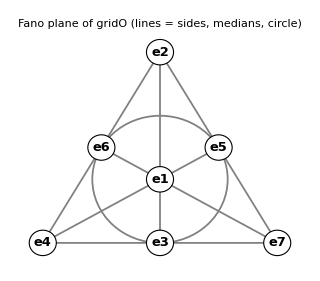

```mathematica
fanoPicture = Module[{pos, lines},
   pos = <|1 -> {0, 0}, 2 -> {0, 2}, 4 -> {-Sqrt[3], -1}, 7 -> {Sqrt[3], -1}, 6 -> {-Sqrt[3]/2, 1/2}, 5 -> {Sqrt[3]/2, 1/2}, 3 -> {0, -1}|>;
   Graphics[{Thickness[0.004], Gray,
     Line[{pos[2], pos[4]}], Line[{pos[4], pos[7]}], Line[{pos[7], pos[2]}],
     Line[{pos[2], pos[3]}], Line[{pos[4], pos[5]}], Line[{pos[7], pos[6]}], Circle[{0, 0}, 1],
     Table[{White, EdgeForm[Black], Disk[pos[k], 0.2], Black, Text[Style["e" <> ToString[k], 13, Bold], pos[k]]}, {k, 1, 7}]},
    ImageSize -> 320, PlotLabel -> Style["Fano plane of gridO (lines = sides, medians, circle)", 12]]];
check["the picture's 7 lines are exactly fanoLines", Sort[Sort /@ {{2, 6, 4}, {4, 3, 7}, {7, 5, 2}, {2, 1, 3}, {4, 1, 5}, {7, 1, 6}, {6, 5, 3}}] == fanoLines]
fanoPicture
```

#### Alternativity, Moufang identities, norm, conjugation, inverse (symbolic proofs)

xs, ys, zs are general octonions with symbolic components a[0..7], b[0..7], c[0..7]. Identities that are linear in some arguments (Moufang) are proven by letting those arguments run over the basis, which is enough by linearity.

```mathematica
check["left alternative: x(xy) == (xx)y (symbolic)", Expand[oMul[xs, oMul[xs, ys]] - oMul[oMul[xs, xs], ys]] === zero8]
check["right alternative: (yx)x == y(xx) (symbolic)", Expand[oMul[oMul[ys, xs], xs] - oMul[ys, oMul[xs, xs]]] === zero8]
check["flexible: (xy)x == x(yx) (symbolic)", Expand[oMul[oMul[xs, ys], xs] - oMul[xs, oMul[ys, xs]]] === zero8]
check["associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)",
  Expand[oAssoc[xs, ys, zs] + oAssoc[ys, xs, zs]] === zero8 && Expand[oAssoc[xs, ys, zs] + oAssoc[xs, zs, ys]] === zero8]
check["power associativity: x(xx) == (xx)x (symbolic)", Expand[oMul[xs, oMul[xs, xs]] - oMul[oMul[xs, xs], xs]] === zero8]
check["Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)",
  And @@ Flatten[Table[With[{xx = ev[A], yy = ev[K]},
      Expand[oMul[zs, oMul[xx, oMul[zs, yy]]] - oMul[oMul[oMul[zs, xx], zs], yy]] === zero8 &&
      Expand[oMul[xx, oMul[zs, oMul[yy, zs]]] - oMul[oMul[oMul[xx, zs], yy], zs]] === zero8 &&
      Expand[oMul[oMul[zs, xx], oMul[yy, zs]] - oMul[oMul[zs, oMul[xx, yy]], zs]] === zero8], {A, 0, 7}, {K, 0, 7}]]]
check["x x̄ == x̄ x == N(x) e[0] (symbolic)",
  Expand[oMul[xs, oConj[xs]] - oNorm2[xs] ev[0]] === zero8 && Expand[oMul[oConj[xs], xs] - oNorm2[xs] ev[0]] === zero8]
check["conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)",
  Expand[oConj[oMul[xs, ys]] - oMul[oConj[ys], oConj[xs]]] === zero8]
check["Re(x) == (x + x̄)/2 == x0", (xs + oConj[xs])/2 == oRe[xs] ev[0] && oRe[xs] === a[0]]
check["norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)",
  Expand[oNorm2[oMul[xs, ys]] - oNorm2[xs] oNorm2[ys]] === 0]
check["inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)",
  Simplify[oMul[xs, oInv[xs]] - ev[0]] === zero8 && Simplify[oMul[oInv[xs], xs] - ev[0]] === zero8]
check["every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ",
  Expand[oMul[xs, xs] - 2 oRe[xs] xs + oNorm2[xs] ev[0]] === zero8]
```

left alternative: x(xy) == (xx)y (symbolic)→True

right alternative: (yx)x == y(xx) (symbolic)→True

flexible: (xy)x == x(yx) (symbolic)→True

associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)→True

power associativity: x(xx) == (xx)x (symbolic)→True

Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)→True

x x̄ == x̄ x == N(x) e[0] (symbolic)→True

conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)→True

Re(x) == (x + x̄)/2 == x0→True

norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)→True

inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)→True

every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ→True

Degen’s eight-square identity, explicitly: the eight components of x y are bilinear forms, and the sum of their squares equals (a0.b2 + … + a7.b2)(b0.b2 + … + b7.b2). Hence N(x) = 0 forces x = 0, and xy = 0 forces x = 0 or y = 0: unlike the split octonions, the octonions have no zero divisors (a division algebra).

```mathematica
TableForm[Thread[{Table["(x y)_" <> ToString[k], {k, 0, 7}], oMul[xs, ys]}]]
```

(x y)_0 | a[0] b[0]-a[1] b[1]-a[2] b[2]-a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]
(x y)_1 | a[1] b[0]+a[0] b[1]+a[3] b[2]-a[2] b[3]+a[5] b[4]-a[4] b[5]-a[7] b[6]+a[6] b[7]
(x y)_2 | a[2] b[0]-a[3] b[1]+a[0] b[2]+a[1] b[3]+a[6] b[4]+a[7] b[5]-a[4] b[6]-a[5] b[7]
(x y)_3 | a[3] b[0]+a[2] b[1]-a[1] b[2]+a[0] b[3]+a[7] b[4]-a[6] b[5]+a[5] b[6]-a[4] b[7]
(x y)_4 | a[4] b[0]-a[5] b[1]-a[6] b[2]-a[7] b[3]+a[0] b[4]+a[1] b[5]+a[2] b[6]+a[3] b[7]
(x y)_5 | a[5] b[0]+a[4] b[1]-a[7] b[2]+a[6] b[3]-a[1] b[4]+a[0] b[5]-a[3] b[6]+a[2] b[7]
(x y)_6 | a[6] b[0]+a[7] b[1]+a[4] b[2]-a[5] b[3]-a[2] b[4]+a[3] b[5]+a[0] b[6]-a[1] b[7]
(x y)_7 | a[7] b[0]-a[6] b[1]+a[5] b[2]+a[4] b[3]-a[3] b[4]-a[2] b[5]+a[1] b[6]+a[0] b[7]

#### Non-associativity and a numerical example

```mathematica
nonAssociativeTriples = Select[Tuples[Range[0, 7], 3], oAssoc[ev[#[[1]]], ev[#[[2]]], ev[#[[3]]]] =!= zero8 &];
check["exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)",
  Length[nonAssociativeTriples] == 168 && AllTrue[nonAssociativeTriples, (Min[#] >= 1 && Length[Union[#]] == 3 && ! MemberQ[fanoLines, Sort[#]]) &]]
check["example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]",
  toE[oMul[oMul[ev[1], ev[2]], ev[4]]] === e[7] && toE[oMul[ev[1], oMul[ev[2], ev[4]]]] === -e[7]]
```

exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)→True

example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]→True

```mathematica
xNum = {1, 2, 0, 0, -1, 0, 0, 3}; yNum = {-2, 0, 1, 0, 0, 1, 0, 0}; zNum = {0, 0, 0, 1, 0, 0, 1, 0};
Grid[{{"x", toE[xNum]}, {"y", toE[yNum]}, {"z", toE[zNum]}, {"x y", toE[oMul[xNum, yNum]]}, {"y x", toE[oMul[yNum, xNum]]},
   {"N(x), N(y), N(x y)", {oNorm2[xNum], oNorm2[yNum], oNorm2[oMul[xNum, yNum]]}}, {"x^-1", toE[oInv[xNum]]},
   {"x x^-1", toE[oMul[xNum, oInv[xNum]]]}, {"(x y) z - x (y z)", toE[oAssoc[xNum, yNum, zNum]]}}, Frame -> All, Alignment -> Left]
```

x | e[0]+2 e[1]-e[4]+3 e[7]
y | -2 e[0]+e[2]+e[5]
z | e[3]+e[6]
x y | -2 e[0]-3 e[1]+4 e[2]-2 e[3]+4 e[4]-2 e[5]-e[6]-6 e[7]
y x | -2 e[0]-5 e[1]-2 e[2]+2 e[3]+4 e[5]+e[6]-6 e[7]
N(x), N(y), N(x y) | {15,6,90}
x^-1 | e[0]/15-(2 e[1])/15+e[4]/15-e[7]/5
x x^-1 | e[0]
(x y) z - x (y z) | -6 e[1]-2 e[2]-6 e[3]+6 e[4]+2 e[5]+6 e[6]+6 e[7]

```mathematica
check["numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]",
  oNorm2[oMul[xNum, yNum]] == oNorm2[xNum] oNorm2[yNum] == 90 && oMul[xNum, oInv[xNum]] == ev[0]]
check["numerical example: x y != y x and (x y) z != x (y z)", oMul[xNum, yNum] != oMul[yNum, xNum] && oAssoc[xNum, yNum, zNum] != zero8]
```

numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]→True

numerical example: x y != y x and (x y) z != x (y z)→True

### 3.5 Cayley–Dickson doubling: 𝕆 = ℍ ⊕ ℓℍ

The span of e[0], e[1], e[2], e[3] — the time direction and the three ordinary space directions x0 … x3 — is a quaternion subalgebra ℍ, and ℓ = e[4] doubles it: e[4+k] = ℓ e[k] (k = 1, 2, 3). Every octonion is x = a + ℓ b with quaternions a = (x0, x1, x2, x3) and b = (x4, x5, x6, x7). Orientation inherited from 4+4.nb: e[1] e[2] = −e[3], so i = e[1], j = e[2], k = −e[3] are Hamilton’s units. With ℓ.b2 = γ the product is

(a, b)(c, d) = (a c + γ d b̄,  ā d + c b),     γ = −1: octonions,   γ = +1: split octonions.

```mathematica
qMul[p1_List, p2_List] := Take[oMul[Join[p1, {0, 0, 0, 0}], Join[p2, {0, 0, 0, 0}]], 4];
qConj[p1_List] := {p1[[1]], -p1[[2]], -p1[[3]], -p1[[4]]};
asPair[xx_List] := {Take[xx, 4], Take[xx, -4]};                       (* x = a + ℓ b  <->  {a, b} *)
cdMul[γ_][{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] + γ qMul[b2, qConj[b1]], qMul[qConj[a1], b2] + qMul[a2, b1]};
check["ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra", And @@ Flatten[Table[Take[oMul[ev[A], ev[K]], -4] == {0, 0, 0, 0}, {A, 0, 3}, {K, 0, 3}]]]
check["ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]",
  And @@ Table[oMul[ev[4], ev[k]] == ev[4 + k], {k, 1, 3}] && oMul[ev[4], ev[4]] == -ev[0]]
check["orientation inherited from 4+4.nb: e[1] e[2] == -e[3]", oMul[ev[1], ev[2]] == -ev[3]]
check["Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)",
  Expand[Flatten[cdMul[-1][asPair[xs], asPair[ys]]] - oMul[xs, ys]] === zero8]
check["Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)",
  Expand[Flatten[cdMul[+1][asPair[xs], asPair[ys]]] - sMul[xs, ys]] === zero8]
```

ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra→True

ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]→True

orientation inherited from 4+4.nb: e[1] e[2] == -e[3]→True

Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)→True

Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)→True

The second formula of [1A], (a,b)(c,d) = (ac − d̄ b, ā d + c b), mixes two conventions. It fails already for x = e[0] + e[4] = (1, 1) and y = e[1] = (i, 0) (no product of two imaginary quaternion units occurs, so the orientation of ℍ does not matter): x.b2 = (0, 2), x.b2y = (0, 2i), but x y = (i, i) and x(xy) = (2i, 2i).

```mathematica
cdPrompt[{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] - qMul[qConj[b2], b1], qMul[qConj[a1], b2] + qMul[a2, b1]};
pm[xx_List, yy_List] := Flatten[cdPrompt[asPair[xx], asPair[yy]]];
promptX = ev[0] + ev[4]; promptY = ev[1];
{toE[pm[pm[promptX, promptX], promptY]], toE[pm[promptX, pm[promptX, promptY]]]}
```

{2 e[5],2 e[1]+2 e[5]}

```mathematica
check["the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]",
  pm[pm[promptX, promptX], promptY] =!= pm[promptX, pm[promptX, promptY]]]
check["... and its norm is not multiplicative (symbolic)", Expand[oNorm2[pm[xs, ys]] - oNorm2[xs] oNorm2[ys]] =!= 0]
```

the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]→True

... and its norm is not multiplicative (symbolic)→True

### 3.6 Octonions versus split octonions

Comparing gridO with gridx44 (relabelled 0-based, eA[B] → e[B−1]): e[A]e[B] (octonion) = s_AB × e[A]e[B] (split), with s_AB = −1 when both A ≥ 4 and B ≥ 4, and s_AB = +1 otherwise. Only products of two “doubled” units change sign, because ℓ.b2 = −1 instead of +1. Over ℂ the two algebras are isomorphic: ϕ(eA[A+1]) = c_A e[A] with c = (1, 1, 1, 1, i, i, i, i).

```mathematica
sAB[A_, K_] := If[A >= 4 && K >= 4, -1, 1];
check["e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7",
  And @@ Flatten[Table[oMul[ev[A], ev[K]] == sAB[A, K] sMul[ev[A], ev[K]], {A, 0, 7}, {K, 0, 7}]]]
cc = {1, 1, 1, 1, I, I, I, I};
φ[xx_List] := cc xx;
check["over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ",
  Expand[φ[sMul[xs, ys]] - oMul[φ[xs], φ[ys]]] === zero8]
check["the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)", Expand[oNorm2[φ[xs]] - sNorm2[xs]] === 0]
```

e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7→True

over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ→True

the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)→True

## 4. Clifford algebras from the octonions: 16×16 matrices

### 4.1 The exact mirror of T16: the Euclidean Clifford algebra Cl(8,0)

Copying the 4+4.nb definition T16[A] = {{0, τbar[A]}, {τ[A], 0}} with τ → τO and τbar → τObar gives real 16×16 matrices T16O[A] whose anticommutators are governed by the octonion norm gO = ID8: they generate Cl(8,0) ≅ ℝ(16). They can be written with the 4+4 matrices alone: T16O[A] = T16[A] for A = 0 … 3 and T16O[k] = T16[k].S44 for k = 4 … 7, where S44 = T16[4].T16[5].T16[6].T16[7] = diag(σ, σ).

```mathematica
Do[T16O[A] = ArrayFlatten[{{0, τObar[A]}, {τO[A], 0}}], {A, 0, 7}];
T16O[8] = Dot @@ Table[T16O[A], {A, 0, 7}];
S44 = T16[4].T16[5].T16[6].T16[7];
check["Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["S44 == diag(σ, σ)", S44 == ArrayFlatten[{{σ, 0}, {0, σ}}]]
check["T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)",
  And @@ Table[T16O[A] == T16[A], {A, 0, 3}] && And @@ Table[T16O[k] == T16[k].S44, {k, 4, 7}]]
check["T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb",
  T16O[8] == T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
```

Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16→True

S44 == diag(σ, σ)→True

T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)→True

T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb→True

### 4.2 The REAL Clifford algebra of 7+1 spacetime: Γ17, Cl(1,7) ≅ ℝ(16)

Definition. Γ17[0] = T16O[0] (time) and Γ17[i] = T16O[0].T16O[i] (i = 1 … 7, space). Then

Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17[[A+1,B+1]] ID16 = −2 η71[[A+1,B+1]] ID16:

time squares to +ID16, each of the seven space directions to −ID16. In block form Γ17[0] = {{0, ID8}, {ID8, 0}} (the same block form as T16[0]) and Γ17[i] = {{τO[i], 0}, {0, τObar[i]}} (block-diagonal). With the 4+4 matrices only: Γ17[0] = T16[0], Γ17[i] = T16[0].T16[i] (i = 1, 2, 3), Γ17[k] = T16[0].T16[k].S44 (k = 4 … 7). All entries are 0 or ±1.

Why this is the Clifford algebra of [1B]. (i) The linear map v ↦ Γ17(v) = Σ v^A Γ17[A] satisfies Γ17(v).b2 = Q(v) ID16 with Q(v) = v.η17.v, so by the universal property of Cl(V,Q) = T(V)/I_Q(V) it extends to an algebra homomorphism Cl(V,Q) → ℝ(16). (ii) The 256 ordered products Γ17[A1]…Γ17[Ak] (A1 < … < Ak) are linearly independent, so the homomorphism is injective; both sides have dimension 256, so it is an isomorphism Cl(1,7) ≅ ℝ(16).

```mathematica
Γ17[0] = T16O[0];
Do[Γ17[i] = T16O[0].T16O[i], {i, 1, 7}];
Γ17[8] = Dot @@ Table[Γ17[A], {A, 0, 7}];
check["7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A + 1, B + 1]] ID16 == -η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ17[A] are REAL: every entry is 0 or ±1", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ17[A]]]], {A, 0, 7}]]
check["block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}",
  Γ17[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17[i] == ArrayFlatten[{{τO[i], 0}, {0, τObar[i]}}], {i, 1, 7}]]
check["built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)",
  Γ17[0] == T16[0] && And @@ Table[Γ17[i] == T16[0].T16[i], {i, 1, 3}] && And @@ Table[Γ17[k] == T16[0].T16[k].S44, {k, 4, 7}]]
check["Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)",
  Transpose[Γ17[0]] == Γ17[0] && And @@ Table[Transpose[Γ17[i]] == -Γ17[i], {i, 1, 7}] &&
  And @@ Table[Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0], {A, 0, 7}]]
```

7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16→True

Γ17[A] are REAL: every entry is 0 or ±1→True

block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}→True

built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)→True

Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)→True

```mathematica
Grid[Partition[Table[Column[{Style["Γ17[" <> ToString[A] <> "]", Bold], MatrixForm[Γ17[A]]}, Alignment -> Center], {A, 0, 7}], 2], Spacings -> {3, 2}]
```

Γ17[0]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
Γ17[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)
Γ17[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | Γ17[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
Γ17[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | Γ17[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

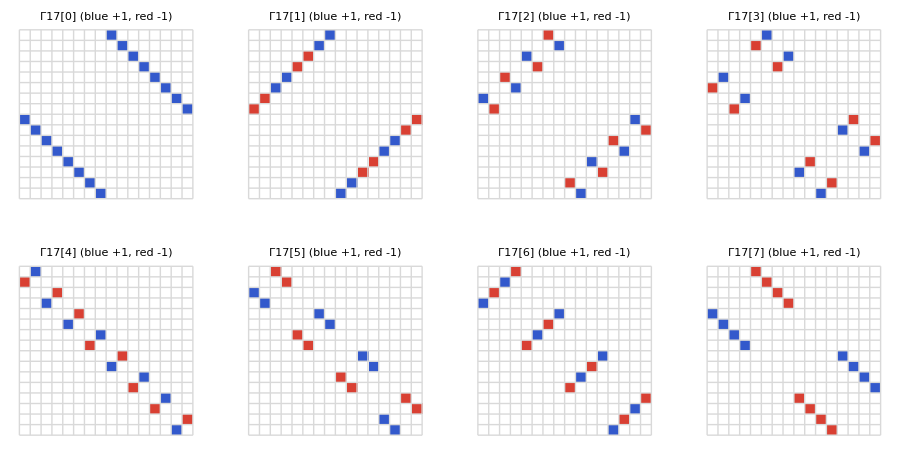

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[Γ17[A], ColorRules -> {1 -> RGBColor[0.2, 0.35, 0.8], -1 -> RGBColor[0.85, 0.25, 0.2], 0 -> White},
     Mesh -> True, MeshStyle -> GrayLevel[0.85], Frame -> False, PlotLabel -> "Γ17[" <> ToString[A] <> "]   (blue +1, red -1)"], {A, 0, 7}], 4], ImageSize -> 900]
```

```mathematica
products256 = Table[Dot @@ Prepend[Γ17 /@ s, ID16], {s, Subsets[Range[0, 7]]}];
check["the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)",
  Length[products256] == 256 && MatrixRank[Flatten /@ products256] == 256]
check["grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)",
  Table[Binomial[8, k], {k, 0, 8}] == {1, 8, 28, 56, 70, 56, 28, 8, 1} && Total[Table[Binomial[8, k], {k, 0, 8}]] == 256 &&
  Table[Count[Subsets[Range[0, 7]], s_ /; Length[s] == k], {k, 0, 8}] == Table[Binomial[8, k], {k, 0, 8}]]
check["Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M", And @@ Table[Tr[products256[[k]]] == 0, {k, 2, 256}]]
check["irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)",
  With[{ns = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] - KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]]},
   Length[ns] == 1 && MatrixRank[{First[ns], Flatten[ID16]}] == 1]]
check["universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X",
  Expand[Sum[X[[A + 1]] Γ17[A], {A, 0, 7}].Sum[X[[A + 1]] Γ17[A], {A, 0, 7}] - (X.η17.X) ID16] === Zero16]
```

the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)→True

grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)→True

Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M→True

irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)→True

universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X→True

### 4.3 The complexified 7+1 realization in the exact block form of 4+4.nb: Γ71

If one insists on the 4+4.nb sign convention, Γ71[A].Γ71[B] + Γ71[B].Γ71[A] = 2 η71[[A+1,B+1]] ID16, complex numbers are unavoidable (section 4.4). The complexification needed is minimal: multiply the time block by i. With τC[0] = τCbar[0] = i ID8 and τC[i] = τO[i], τCbar[i] = τObar[i] (i = 1 … 7),

Γ71[A] = {{0, τCbar[A]}, {τC[A], 0}},

which is literally the formula T16[A] = {{0, τbar[A]}, {τ[A], 0}} of 4+4.nb. Equivalently Γ71[0] = i T16[0] and Γ71[k] = T16O[k] (k = 1 … 7). Γ71 is equivalent to i Γ17: Γ71[A] = S.(i Γ17[A]).S⁻.b9 with the unitary matrix S = (ID16 − i Γ17[0])/√2.

```mathematica
τC[0] = I ID8; τCbar[0] = I ID8;
Do[τC[i] = τO[i]; τCbar[i] = τObar[i], {i, 1, 7}];
Do[Γ71[A] = ArrayFlatten[{{0, τCbar[A]}, {τC[A], 0}}], {A, 0, 7}];
Γ71[8] = Dot @@ Table[Γ71[A], {A, 0, 7}];
check["7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex",
  Γ71[0] == I T16[0] && And @@ Table[Γ71[k] == T16O[k], {k, 1, 7}]]
Ssim = (ID16 - I Γ17[0])/Sqrt[2];
check["S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]",
  Simplify[Ssim.ConjugateTranspose[Ssim]] == ID16 && And @@ Table[Simplify[Ssim.(I Γ17[A]).Inverse[Ssim] - Γ71[A]] == Zero16, {A, 0, 7}]]
```

7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16→True

Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex→True

S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]→True

### 4.4 Theorem: with η71 there is no real 16×16 realization, because Cl(7,1) ≅ ℍ(8)

Theorem. There are no real 16×16 matrices R[0], …, R[7] with R[A].R[B] + R[B].R[A] = 2 η71[[A+1,B+1]] ID16. Reordering, renaming or re-signing the indices does not help, because none of these changes the signature (7,1).

Proof. The complexified Clifford algebra is Cl_8(ℂ) ≅ ℂ(16), which has exactly one irreducible module, ℂ^16. If real R[A] existed, they and the complex Γ71[A] of section 4.3 would both be 16-dimensional modules, so R[A] = T.Γ71[A].T⁻.b9 for some invertible complex T. Complex conjugation of this equation (R is real) gives M.Conjugate[Γ71[A]] = Γ71[A].M with M = T⁻.b9.Conjugate[T], and then M.Conjugate[M] = ID16. By Schur’s lemma all such intertwiners M form a one-dimensional space; the computation below shows that it is spanned by M0 = Γ17[8] (the volume element) and that M0.Conjugate[M0] = −ID16. Hence M = c M0 and M.Conjugate[M] = −|c|.b2 ID16 ≠ ID16, a contradiction. ∎

The sign of M.Conjugate[M] is a Frobenius–Schur-type indicator: +1 means the complex 16-dimensional module has a real form (the algebra is ℝ(16)), −1 means it is quaternionic (the algebra is ℍ(8), whose smallest real module is ℍ^8 = ℝ^32). For η17 the indicator is +1, in agreement with the real matrices Γ17 of section 4.2.

```mathematica
intertwiners[gs_List] := Module[{n = Length[First[gs]], sys},
   sys = Join @@ Table[KroneckerProduct[IdentityMatrix[n], Transpose[Conjugate[g]]] - KroneckerProduct[g, IdentityMatrix[n]], {g, gs}];
   Partition[#, n] & /@ NullSpace[sys]];       (* all M with M.Conjugate[g] == g.M for every g in gs *)
indicator[gs_List] := Module[{M = First[intertwiners[gs]], P}, P = M.Conjugate[M];
   If[P == P[[1, 1]] IdentityMatrix[Length[P]], Sign[P[[1, 1]]], "not scalar"]];
M71 = intertwiners[Table[Γ71[A], {A, 0, 7}]];
check["Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space", Length[M71] == 1]
check["... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16",
  Γ17[8] == ArrayFlatten[{{0, -ID8}, {ID8, 0}}] &&
  MatrixRank[{Flatten[First[M71]], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16 &&
  And @@ Table[Γ17[8].Conjugate[Γ71[A]] == Γ71[A].Γ17[8], {A, 0, 7}]]
check["indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation",
  indicator[Table[Γ71[A], {A, 0, 7}]] == -1]
check["indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)",
  indicator[Table[Γ17[A], {A, 0, 7}]] == 1]
```

Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space→True

... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16→True

indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation→True

indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)→True

### 4.5 A real realization of Cl(7,1) needs 32×32 matrices

With ϵ = {{0, 1}, {−1, 0}} (real, ϵ.ϵ = −ID2), Γ71R32[A] = ϵ ⊗ Γ17[A] are real 32×32 matrices satisfying the η71 relation. Their commutant (all matrices commuting with every Γ71R32[A]) is spanned by ID32, Qi = ϵ⊗ID16, Qj = σ₁⊗Γ17[8], Qk = σ₃⊗Γ17[8], with Qi.b2 = Qj.b2 = Qk.b2 = −ID32 and Qi.Qj = Qk: the quaternions. This is Cl(7,1) ≅ ℍ(8) acting on ℝ^32 = ℍ^8.

```mathematica
ϵ2 = {{0, 1}, {-1, 0}};
Do[Γ71R32[A] = KroneckerProduct[ϵ2, Γ17[A]], {A, 0, 7}];
check["REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32",
  And @@ Flatten[Table[(Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A + 1, B + 1]] ID32, {A, 0, 7}, {B, 0, 7}]] &&
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ71R32[A]]]], {A, 0, 7}]]
Qi = KroneckerProduct[ϵ2, ID16]; Qj = KroneckerProduct[{{0, 1}, {1, 0}}, Γ17[8]]; Qk = KroneckerProduct[{{1, 0}, {0, -1}}, Γ17[8]];
check["Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi",
  And @@ Flatten[Table[q.Γ71R32[A] == Γ71R32[A].q, {q, {Qi, Qj, Qk}}, {A, 0, 7}]] &&
  Qi.Qi == -ID32 && Qj.Qj == -ID32 && Qk.Qk == -ID32 && Qi.Qj == Qk && Qj.Qi == -Qk]
{commutantTime, commutantBasis} = AbsoluteTiming[NullSpace[Join @@ Table[
       KroneckerProduct[SparseArray[ID32], SparseArray[Transpose[Γ71R32[A]]]] - KroneckerProduct[SparseArray[Γ71R32[A]], SparseArray[ID32]], {A, 0, 7}]]];
check["the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ",
  Length[commutantBasis] == 4 && MatrixRank[Join[Normal[commutantBasis], Flatten /@ {ID32, Qi, Qj, Qk}]] == 4]
commutantTime
```

REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32→True

Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi→True

the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ→True

1.03497

### 4.6 Volume elements and chirality

In 4+4.nb the volume element T16[8] = T16[0]…T16[7] = diag(−ID8, ID8) squares to +ID16 and gives the real chiral projectors PL44, PR44; the same holds for T16O[8]. For the real 7+1 matrices the volume element Γ17[8] squares to −ID16: it is a complex structure, so there is NO real chirality projector. The real 16-component spinors of 7+1 spacetime (the vectors of ℝ^16 on which the real matrices Σ17[A,B] of section 5.1 act) cannot be split into real Weyl halves; with J = Γ17[8] (which commutes with all Σ17[A,B]) as the multiplication by i, the real 16-dimensional spin module is one complex 8-dimensional Weyl module. With complex numbers the chirality matrix is χ17 = i Γ17[8]; in the basis of Γ71 it is χ71 = −i Γ71[8] = T16[8], so the 7+1 chiral projectors are literally PL44 and PR44 of 4+4.nb.

```mathematica
check["Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1",
  Γ17[8].Γ17[8] == -ID16 && And @@ Table[Γ17[8].Γ17[A] == -Γ17[A].Γ17[8], {A, 0, 7}]]
χ71 = -I Γ71[8];
check["Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)",
  Γ71[8].Γ71[8] == -ID16 && χ71 == T16O[8] == T16[8]]
PL71 = (ID16 - χ71)/2; PR71 = (ID16 + χ71)/2;
check["7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]",
  PL71 == PL44 && PR71 == PR44 && And @@ Table[χ71.Γ71[A] == -Γ71[A].χ71, {A, 0, 7}]]
χ17 = I Γ17[8]; PL17 = (ID16 - χ17)/2; PR17 = (ID16 + χ17)/2;
check["complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each",
  PL17 + PR17 == ID16 && PL17.PL17 == PL17 && PR17.PR17 == PR17 && PL17.PR17 == Zero16 && MatrixRank[PL17] == 8 && MatrixRank[PR17] == 8]
```

Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1→True

Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)→True

7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]→True

complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each→True

### 4.7 What the octonions do: Γ(x).b2 = Re(x x), and alternativity

For x = Σ x^A e[A] with components equal to the coordinates X: Re(x x) = x0.b2 − x1.b2 − … − x7.b2 = X.η17.X, the 7+1 interval, and Γ17(x).b2 = Re(x x) ID16. In the octonion basis (rotate both 8-blocks by EO) the generators are Γ17e[0] = {{0, ID8}, {ID8, 0}} and Γ17e[i] = {{LO[i], 0}, {0, −LO[i]}}. Write x = x0 e[0] + x⃗ with the imaginary part x⃗ = x1 e[1] + … + x7 e[7] (xImag in the code); then on Ψ = (ψ1, ψ2) ∈ 𝕆 ⊕ 𝕆:

Γ17e(x) Ψ = (x0 ψ2 + x⃗ ψ1,  x0 ψ1 − x⃗ ψ2)   (octonion products),

Γ17e(x).b2 Ψ = (x0.b2 ψ1 + x⃗(x⃗ ψ1),  x0.b2 ψ2 + x⃗(x⃗ ψ2)) = (x0.b2 − |x⃗|.b2) Ψ,

where the last step is exactly alternativity: x⃗(x⃗ ψ) = (x⃗ x⃗) ψ = −|x⃗|.b2 ψ. The same formula with the norm form instead of Re(x x) gives T16O(x).b2 = N(x) ID16, and in 4+4.nb T16(x).b2 = X.η4488.X ID16.

```mathematica
check["Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)", Expand[oRe[oMul[X, X]] - X.η17.X] === 0]
EO16 = ArrayFlatten[{{EO, 0}, {0, EO}}];
Do[Γ17e[A] = FullSimplify[EO16.Γ17[A].Transpose[EO16]], {A, 0, 7}];
check["octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}",
  Γ17e[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17e[i] == ArrayFlatten[{{LO[i], 0}, {0, -LO[i]}}], {i, 1, 7}]]
xImag = Join[{0}, Rest[X]]; ψs = Array[ψ, 8, 0];
check["alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)", Expand[oMul[xImag, oMul[xImag, ψs]] + (Rest[X].Rest[X]) ψs] === zero8]
check["T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)",
  Expand[Sum[X[[A + 1]] T16O[A], {A, 0, 7}].Sum[X[[A + 1]] T16O[A], {A, 0, 7}] - (X.gO.X) ID16] === Zero16 &&
  Expand[Sum[X[[A + 1]] T16[A], {A, 0, 7}].Sum[X[[A + 1]] T16[A], {A, 0, 7}] - (X.η4488.X) ID16] === Zero16]
```

Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)→True

octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}→True

alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)→True

T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)→True

## 5. Examples that test everything

### 5.1 The Lorentz algebra so(1,7)

The 28 real matrices Σ17[A,B] = (Γ17[A].Γ17[B] − Γ17[B].Γ17[A])/4 (A < B) generate Spin(1,7). They satisfy

[Σ17[A,B], Γ17[K]] = η17[[B+1,K+1]] Γ17[A] − η17[[A+1,K+1]] Γ17[B],

[Σ_AB, Σ_KL] = η_BK Σ_AL − η_AK Σ_BL − η_BL Σ_AK + η_AL Σ_BK   (η = η17).

```mathematica
Σ17[A_, B_] := (Γ17[A].Γ17[B] - Γ17[B].Γ17[A])/4;
pairs = Subsets[Range[0, 7], {2}];
check["28 real generators Σ17[A,B] (A < B), linearly independent", Length[pairs] == 28 && MatrixRank[Flatten[Σ17 @@ #] & /@ pairs] == 28]
check["[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]",
  And @@ Flatten[Table[Σ17[A, B].Γ17[K] - Γ17[K].Σ17[A, B] == η17[[B + 1, K + 1]] Γ17[A] - η17[[A + 1, K + 1]] Γ17[B], {A, 0, 7}, {B, 0, 7}, {K, 0, 7}]]]
check["so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK",
  And @@ Flatten[Table[With[{A = p1[[1]], B = p1[[2]], K = p2[[1]], L = p2[[2]]},
      Σ17[A, B].Σ17[K, L] - Σ17[K, L].Σ17[A, B] ==
       η17[[B + 1, K + 1]] Σ17[A, L] - η17[[A + 1, K + 1]] Σ17[B, L] - η17[[B + 1, L + 1]] Σ17[A, K] + η17[[A + 1, L + 1]] Σ17[B, K]], {p1, pairs}, {p2, pairs}]]]
check["the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)",
  And @@ Table[Γ17[8].(Σ17 @@ p) == (Σ17 @@ p).Γ17[8], {p, pairs}]]
```

28 real generators Σ17[A,B] (A < B), linearly independent→True

[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]→True

so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK→True

the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)→True

### 5.2 A boost along x1 and a rotation in the x4–x5 plane

Because (Γ17[0].Γ17[1]).b2 = +ID16 and (Γ17[4].Γ17[5]).b2 = −ID16, the exponentials are

S(β) = exp(β Σ17[0,1]) = cosh(β/2) ID16 + sinh(β/2) Γ17[0].Γ17[1],    R(θ) = exp(θ Σ17[4,5]) = cos(θ/2) ID16 + sin(θ/2) Γ17[4].Γ17[5],

both real. Conjugation by them acts on the generators as a Lorentz transformation, S.Γ17[K].S⁻.b9 = Σ_B Λ[[B+1,K+1]] Γ17[B], with Λ read off from traces: Λ[[B+1,K+1]] = Tr[Γ17^B.S.Γ17[K].S⁻.b9]/16, Γ17^B = η17[[B+1,B+1]] Γ17[B].

```mathematica
Sβ = Cosh[β/2] ID16 + Sinh[β/2] Γ17[0].Γ17[1];  Sβinv = Cosh[β/2] ID16 - Sinh[β/2] Γ17[0].Γ17[1];
Rθ = Cos[θ/2] ID16 + Sin[θ/2] Γ17[4].Γ17[5];  Rθinv = Cos[θ/2] ID16 - Sin[θ/2] Γ17[4].Γ17[5];
check["S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16",
  Simplify[D[Sβ, β] - Σ17[0, 1].Sβ] == Zero16 && (Sβ /. β -> 0) == ID16 &&
  Simplify[D[Rθ, θ] - Σ17[4, 5].Rθ] == Zero16 && (Rθ /. θ -> 0) == ID16 &&
  Simplify[Sβ.Sβinv] == ID16 && Simplify[Rθ.Rθinv] == ID16]
Λboost = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Sβ.Γ17[K].Sβinv]/16], {B, 0, 7}, {K, 0, 7}];
Λrot = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Rθ.Γ17[K].Rθinv]/16], {B, 0, 7}, {K, 0, 7}];
{MatrixForm[Λboost], MatrixForm[Λrot]}
```

S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16→True

{(Cosh[β] | -Sinh[β] | 0 | 0 | 0 | 0 | 0 | 0
-Sinh[β] | Cosh[β] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[θ] | -Sin[θ] | 0 | 0
0 | 0 | 0 | 0 | Sin[θ] | Cos[θ] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
check["S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1",
  And @@ Table[Simplify[Sβ.Γ17[K].Sβinv - Sum[Λboost[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λboost == ReplacePart[IdentityMatrix[8], {{1, 1} -> Cosh[β], {1, 2} -> -Sinh[β], {2, 1} -> -Sinh[β], {2, 2} -> Cosh[β]}]]
check["R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane",
  And @@ Table[Simplify[Rθ.Γ17[K].Rθinv - Sum[Λrot[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λrot == ReplacePart[IdentityMatrix[8], {{5, 5} -> Cos[θ], {5, 6} -> -Sin[θ], {6, 5} -> Sin[θ], {6, 6} -> Cos[θ]}]]
check["both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17",
  Simplify[Transpose[Λboost].η17.Λboost - η17] == ConstantArray[0, {8, 8}] &&
  Simplify[Transpose[Λrot].η17.Λrot - η17] == ConstantArray[0, {8, 8}]]
```

S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1→True

R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane→True

both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17→True

### 5.3 The 7+1 Dirac operator squares to the 7+1 wave operator

With Γ17^A = η17^{AA} Γ17[A] (index raised with the inverse metric) the Dirac operator is Γ17^A ∂_A, acting on 16-component fields Ψ(x0, …, x7). Its square is the wave operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 times ID16, for completely arbitrary functions:

```mathematica
η17inv = Inverse[η17];
Γ17up[A_] := η17inv[[A + 1, A + 1]] Γ17[A];
Ψfun = Table[f[k] @@ X, {k, 1, 16}];
DiracOp17[ψψ_] := Sum[Γ17up[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
waveOp17[ψψ_] := Sum[η17inv[[A + 1, A + 1]] D[ψψ, {X[[A + 1]], 2}], {A, 0, 7}];
check["(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7",
  Simplify[DiracOp17[DiracOp17[Ψfun]] - waveOp17[Ψfun]] === ConstantArray[0, 16]]
```

(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7→True

### 5.4 Spinors on the mass shell: real amplitudes

Take the momentum p = (3, 2, 2, 0, 0, 0, 0, 0) (contravariant components p^A) and mass m = 1: p.η17.p = 9 − 4 − 4 = 1 = m.b2. With pslash = Σ p^A Γ17[A] we have pslash.pslash = m.b2 ID16, so pslash has eigenvalues ±m, each 8 times. Because pslash is a REAL matrix, the momentum-space Dirac equation (pslash − m) w = 0 has an 8-dimensional space of REAL solutions w (the spinor amplitudes), and each w gives the plane wave Ψ = w e^{−i p·x}, p·x = p.η17.X, of the Dirac equation (i Γ17^A ∂_A − m) Ψ = 0. The plane wave itself is complex; section 5.5 explains which real spinor FIELDS exist.

```mathematica
pvec = {3, 2, 2, 0, 0, 0, 0, 0}; mass = 1;
pslash = Sum[pvec[[A + 1]] Γ17[A], {A, 0, 7}];
realAmplitudes = NullSpace[pslash - mass ID16];
check["p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16", pvec.η17.pvec == mass^2 && pslash.pslash == mass^2 ID16]
check["(pslash - m) w == 0 has 8 linearly independent REAL solutions w", Length[realAmplitudes] == 8 &&
  AllTrue[Flatten[realAmplitudes], MatchQ[#, _Integer | _Rational] &] && MatrixRank[realAmplitudes] == 8]
Ψwave = First[realAmplitudes] Exp[-I (pvec.η17.X)];
check["Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0", Simplify[I DiracOp17[Ψwave] - mass Ψwave] === ConstantArray[0, 16]]
MatrixForm[realAmplitudes]
```

p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16→True

(pslash - m) w == 0 has 8 linearly independent REAL solutions w→True

Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0→True

(2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-2 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | -2 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 2 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 5.5 Real spinor fields: massless with Γ17, massive with the real 32×32 matrices

A real massive FIELD is a different matter. The operator i Γ17^A ∂_A is imaginary, so a real Ψ cannot solve (i Γ17^A ∂_A − m) Ψ = 0. A real equation (G^A ∂_A − m) Ψ = 0 with real 16×16 matrices G[A] implies the Klein–Gordon equation, (G^A ∂_A + m)(G^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2), only if (G^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2), i.e. only if the G[A] satisfy the η71 relation (time squaring to −1); section 4.4 proves that no real 16×16 matrices do. The remaining real option, (Γ17^A ∂_A − m J) Ψ = 0, has the Klein–Gordon operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2 as its square only if the real matrix J anticommutes with every Γ17[A] and J.J = +ID16. But the matrices anticommuting with all Γ17[A] are exactly the multiples c Γ17[8] (checked below), whose squares −c.b2 ID16 are negative: the square is then ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 − c.b2 m.b2, a tachyon. So, with 16 real components:

massless real fields exist: for a null momentum k (k.η17.k = 0) the real equation kslash w = 0 has 8 real solutions, and Ψ = w cos(k·x) is a REAL solution of Γ17^A ∂_A Ψ = 0;

massive real fields do not exist; they need 32 real components.

The real 32×32 matrices Γ71R32[A] of section 4.5 satisfy the η71 relation, and with them a real massive field exists. With Γ71R32^A = η71^{AA} Γ71R32[A] one has (Γ71R32^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2) ID32, hence (Γ71R32^A ∂_A + m)(Γ71R32^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2): the correct Klein–Gordon operator. For p as in section 5.4, P = Σ p^A Γ71R32[A] satisfies P.P = p.η71.p ID32 = −m.b2 ID32, and for ANY 32 real constants w

Ψ = w cos(p·x) + (P.w/m) sin(p·x)

is a REAL solution of (Γ71R32^A ∂_A − m) Ψ = 0. This is the price of a real massive spinor in 7+1 spacetime: 32 real components, the quaternionic module ℍ^8 = ℝ^32 of Cl(7,1) ≅ ℍ(8).

```mathematica
antiCommutant = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] + KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]];
check["the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16",
  Length[antiCommutant] == 1 && MatrixRank[{First[antiCommutant], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16]
kvec = {1, 1, 0, 0, 0, 0, 0, 0};
kslash = Sum[kvec[[A + 1]] Γ17[A], {A, 0, 7}];
realNull = NullSpace[kslash];
ΨmasslessReal = First[realNull] Cos[kvec.η17.X];
check["null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions",
  kvec.η17.kvec == 0 && kslash.kslash == Zero16 && Length[realNull] == 8 && MatrixRank[realNull] == 8 &&
  AllTrue[Flatten[realNull], MatchQ[#, _Integer | _Rational] &]]
check["Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0",
  FreeQ[ΨmasslessReal, _Complex] && Simplify[DiracOp17[ΨmasslessReal]] === ConstantArray[0, 16]]
```

the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16→True

null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions→True

Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0→True

```mathematica
η71inv = Inverse[η71];
DiracOp71R32[ψψ_] := Sum[η71inv[[A + 1, A + 1]] Γ71R32[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
Ψfun32 = Table[g32[k] @@ X, {k, 1, 32}];
check["(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7",
  Simplify[DiracOp71R32[DiracOp71R32[Ψfun32]] + waveOp17[Ψfun32]] === ConstantArray[0, 32]]
pslash32 = Sum[pvec[[A + 1]] Γ71R32[A], {A, 0, 7}];
w32 = Array[w, 32];
Ψ32 = w32 Cos[pvec.η17.X] + (pslash32.w32/mass) Sin[pvec.η17.X];
check["p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32", pvec.η71.pvec == -mass^2 && pslash32.pslash32 == -mass^2 ID32]
check["Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0",
  FreeQ[Ψ32, _Complex] && Simplify[DiracOp71R32[Ψ32] - mass Ψ32] === ConstantArray[0, 32]]
check["... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0",
  Simplify[waveOp17[Ψ32] + mass^2 Ψ32] === ConstantArray[0, 32]]
```

(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7→True

p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32→True

Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0→True

... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0→True

### 5.6 All nine signatures p + q = 8, and the corrected table of [1B]

For every signature, take the first p generators from T16O and the remaining q as i T16O (complex 16×16 matrices satisfying the Clifford relation with p generators squaring to +1 and q to −1). The indicator of section 4.4 decides whether a real form exists (ℝ(16)) or not (ℍ(8)). Explicit REAL 16×16 generators exist exactly in the ℝ(16) cases and are built here from the 4+4 and octonion matrices: (8,0) T16O; (5,3) Γ53 (the split-octonion analogue of Γ17: T16[0], T16[0].T16[i], whose quadratic form is Re(x x) of the split octonions); (4,4) T16 of 4+4.nb; (1,7) Γ17; (0,8) Γ08 = T16O[8].T16O[A].

```mathematica
Γ53[0] = T16[0]; Do[Γ53[i] = T16[0].T16[i], {i, 1, 7}];
η53 = DiagonalMatrix[{1, -1, -1, -1, 1, 1, 1, 1}];
check["split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices",
  Expand[sMul[X, X][[1]] - X.η53.X] === 0 &&
  And @@ Flatten[Table[(Γ53[A].Γ53[B] + Γ53[B].Γ53[A])/2 == η53[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
Do[Γ08[A] = T16O[8].T16O[A], {A, 0, 7}];
check["Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices",
  And @@ Flatten[Table[(Γ08[A].Γ08[B] + Γ08[B].Γ08[A])/2 == -KroneckerDelta[A, B] ID16, {A, 0, 7}, {B, 0, 7}]]]
gens[p_] := Table[If[A < p, T16O[A], I T16O[A]], {A, 0, 7}];
check["gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8",
  And @@ Flatten[Table[With[{g = gens[p]}, (g[[A + 1]].g[[B + 1]] + g[[B + 1]].g[[A + 1]])/2 == If[A == B, If[A < p, 1, -1], 0] ID16], {p, 0, 8}, {A, 0, 7}, {B, 0, 7}]]]
classification = Table[{p, 8 - p, indicator[gens[p]]}, {p, 8, 0, -1}];
claimed1B = {"ℝ(16)", "ℝ(16)", "ℍ(8)", "ℂ(16)", "ℝ(16)", "ℂ(16)", "ℍ(8)", "ℝ(16)", "ℝ(16)"};
correct = If[# == 1, "ℝ(16)", "ℍ(8)"] & /@ classification[[All, 3]];
Grid[Prepend[Table[{"Cl(" <> ToString[classification[[k, 1]]] <> "," <> ToString[classification[[k, 2]]] <> ")",
     StringJoin[Riffle[Join[Table["+", classification[[k, 1]]], Table["-", classification[[k, 2]]]], ","]],
     classification[[k, 3]], correct[[k]], claimed1B[[k]], If[correct[[k]] == claimed1B[[k]], "agrees", "WRONG in [1B]"]}, {k, 1, 9}],
   {"algebra", "squares of the generators", "indicator", "correct (this notebook)", "claimed in [1B]", "status"}],
  Frame -> All, Background -> {None, {LightGray}}]
```

split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices→True

Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices→True

gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8→True

algebra | squares of the generators | indicator | correct (this notebook) | claimed in [1B] | status
Cl(8,0) | +,+,+,+,+,+,+,+ | 1 | ℝ(16) | ℝ(16) | agrees
Cl(7,1) | +,+,+,+,+,+,+,- | -1 | ℍ(8) | ℝ(16) | WRONG in [1B]
Cl(6,2) | +,+,+,+,+,+,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(5,3) | +,+,+,+,+,-,-,- | 1 | ℝ(16) | ℂ(16) | WRONG in [1B]
Cl(4,4) | +,+,+,+,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(3,5) | +,+,+,-,-,-,-,- | -1 | ℍ(8) | ℂ(16) | WRONG in [1B]
Cl(2,6) | +,+,-,-,-,-,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(1,7) | +,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(0,8) | -,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees

```mathematica
check["classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)",
  classification[[All, 3]] == {1, -1, -1, 1, 1, -1, -1, 1, 1}]
check["every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[g]]], {g, Flatten[{Table[T16O[A], {A, 0, 7}], Table[Γ53[A], {A, 0, 7}], Table[T16[A], {A, 0, 7}], Table[Γ17[A], {A, 0, 7}], Table[Γ08[A], {A, 0, 7}]}, 1]}]]
check["ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256", 2*16^2 == 512 && 2^8 == 256]
```

classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)→True

every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)→True

ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256→True

## 6. Summary of all checks

```mathematica
Length[checks]
```

128

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True